```mathematica
delPhi = 1/8;
d=3;
Clear[d,delPhi]
```

```mathematica
rhoNu= rhoDiscl/.l->0;
kNu= Kldel/.{l->0,del->d/2+I nu};
```

```mathematica
rhoNu/.nu->1//N
```

0.00349143+0. ⅈ

```mathematica
kNu /. nu->//N
```

0.471234-1.38778×10^-17 ⅈ

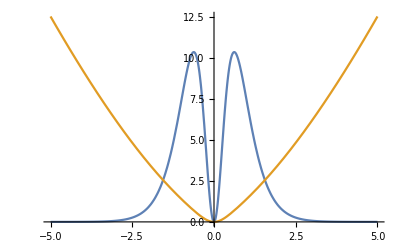

```mathematica
Plot[{kNu/.{nu->x,d->3,delPhi->1.1},rhoNu/.{nu->x,d->3,delPhi->1.1}},{x,-5,5}]
```

```mathematica
param=Ndel^2/(4 Gamma[delPhi]^4)Sin[Pi/2(4 delPhi -d)]/.{del->delPhi}
```

(π^(-2-d) Gamma[d/2-delPhi]^2 Sin[1/2 (-d+4 delPhi) π])/(64 Gamma[delPhi]^2)

```mathematica
param/.{d->2,delPhi->0.8}//N
```

0.00237211

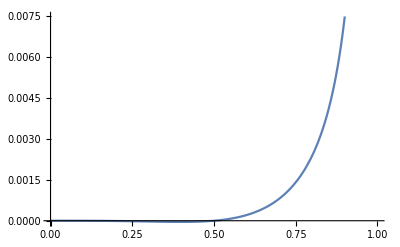

```mathematica
Plot[param/.{d->2,delPhi->x},{x,0.00001,2/2-0.00001}]
```

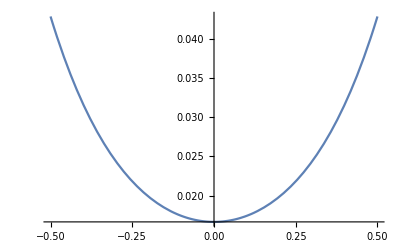

```mathematica
Plot[rhoNu/kNu/.{nu->x,d->2,delPhi->0.8},{x,-0.5,0.5}]
```